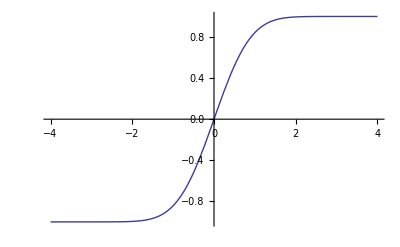

```mathematica
Plot[Erf[x],{x,-4.,4.}]
```

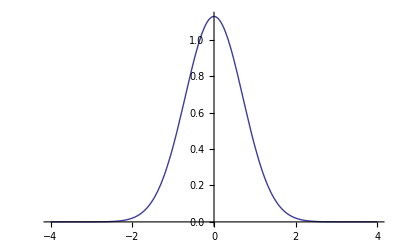

```mathematica
Plot[(2 ⅇ^(-x^2))/(√π),{x,-4.,4},PlotRange->All]
```

```mathematica
S[E_,A_,E0_,W_,Y0_]:=A ×.5(Erf[(E-E0)/W]+1)+Y0
```

```mathematica
D[S[EE,A,E0,W,Y0],A]
D[S[EE,A,E0,W,Y0],E0]
D[S[EE,A,E0,W,Y0],W]
D[S[EE,A,E0,W,Y0],Y0]
```

0.5 (1+Erf[(-E0+EE)/W])

-(0.56419 A ⅇ^(-(-E0+EE)^2/W^2))/W

-(0.56419 A ⅇ^(-(-E0+EE)^2/W^2) (-E0+EE))/W^2

1